Standard form

```mathematica
sol=NDSolve[{ψ'''[s]==-1/2 ψ'[s]^3-(2 Cos[ψ[s]])/r[s] ψ''[s]+(3 Sin[ψ[s]] ψ'[s]^2)/(2r[s])+(3 Cos[ψ[s]]^2-1)/(2 r[s]^2)ψ'[s]-(Cos[ψ[s]]^2+1)/(2 r[s]^3)Sin[ψ[s]]+σ (ψ'[s]+Sin[ψ[s]]/r[s]),r'[s]==Cos[ψ[s]],r[0]==20,ψ[0]==ArcSin[1/(2 π*20)]-ϵ,ψ'[0]==-(Sin[ArcSin[1/(2 π*20)]-ϵ])/20,ψ''[0]==-1/2(Sin[ArcSin[1/(2 π*20)]-ϵ]/20)^2 Tan[ArcSin[1/(2 π*20)]-ϵ]+Cos[(ArcSin[1/(2 π*20)]-ϵ)/20]/20 20/(-Sin[ArcSin[1/(2 π*20)]-ϵ])+((Cos[(ArcSin[1/(2 π*20)]-ϵ)/20]^2+1)/800+σ)Tan[ArcSin[1/(2 π*20)]-ϵ] - f/20}/.{ϵ->0.0001,f->0.001,σ->1/2},{ψ[s],r[s]},{s,-100,0},MaxStepSize->0.01,AccuracyGoal->5,PrecisionGoal->4];
```

system form

NDSolve::ndsz: At s == -68.4729, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {-69.9986} lies outside the range of data in the interpolating function. Extrapolation will be used.

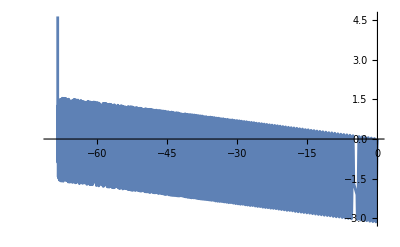

```mathematica
Plot[Evaluate[ψ[s]/.sol],{s,-68.48,0}]
```